# Karol Peszek - Zestaw 2

Zadanie 1.

```mathematica
(*define the sequences*)
a[n_] := (Sin[(n + 1/2) * Pi]) * n^3 - n^2;
b[n_]:= Cos[n * Pi]* n^2 + Sin[2n * Pi]* n^3;
c[n_]:= (3n^2 + 11)/(n^2 * (1 + 3/n^2)^(n^2 + 7));
d[n_]:= ((2n + 5)/(2n - 3))^n;
e[n_]:= (n^3 - 4n^2)^(1/3) - n;
```

```mathematica
(*calculate desired limits*)
```

```mathematica
Limit[a[n], n -> Infinity]
```

Indeterminate

```mathematica
Limit[b[n], n -> Infinity]
```

Indeterminate

```mathematica
Limit[c[n], n -> Infinity]
```

3/ⅇ^3

```mathematica
Limit[d[n], n -> Infinity]
```

ⅇ^4

```mathematica
Limit[e[n], n -> Infinity]
```

-4/3

Zadanie 2.

```mathematica
Limit[(Sin[x]^2)/(1 - Cos[x]), x -> 0]
```

2

```mathematica
Limit[((Sqrt[x + 1] - Sqrt[x - 1])/ 2x), x -> 0]
```

0

```mathematica
Limit[(Log[x^2 + 10] / Log[x^8 + 100]), x -> Infinity]
```

1/4

```mathematica
Limit[(x^2 -5x + 4)/(x * (x - 5)), x -> Infinity]
```

1

```mathematica
Limit[(x - 2)/(x^2 - 4)^ 2, x -> 2, Direction->-1]
```

∞

```mathematica
Limit[(x - 2) / (x^2 - 4)^2, x -> 2, Direction->1]
```

∞

Zadanie 3

```mathematica
(*define the function*)
f[x_]:=Piecewise[{{(Sin[x]^2/(1-Cos[x])),x<0},{(1+3 a) E^(a*x),x>=0}}];
```

```mathematica
left = Limit[f[x], x -> 0, Direction -> -1];
right = Limit[f[x], x -> 0, Direction-> 1];
```

```mathematica
Solve[left == right, a]
```

{{a→1/3}}

Zadanie 4.

```mathematica
(*define functions*)
ClearAll[f]
f[x_] := x^x;
```

```mathematica
g[x_] := x^(2x) * (1 + Sqrt[x^2 - 2])/(4 - Log[1 - x^4]);
```

```mathematica
(*calcualte derivatives*)
```

```mathematica
D[f[x], x]
```

x^x (1+Log[x])

```mathematica
D[g[x], x]
```

-(4 x^(3+2 x) (1+√(-2+x^2)))/((1-x^4) (4-Log[1-x^4])^2)+x^(1+2 x)/(√(-2+x^2) (4-Log[1-x^4]))+(x^(2 x) (1+√(-2+x^2)) (2+2 Log[x]))/(4-Log[1-x^4])

Zadanie 5.

```mathematica
(*define the function*)
ClearAll[f]
f[x_] := FullSimplify[(Log[x / (x + E)^2])^ 4];
```

```mathematica
FullSimplify[D[f[x], {x, 1}] /. x -> E]
```

0

```mathematica
FullSimplify[D[f[x], {x, 2}] /. x -> E]
```

(2 (1+Log[4])^3)/ⅇ^2

```mathematica
FullSimplify[D[f[x], {x, 3}] /. x -> E]
```

-(6 (1+Log[4])^3)/ⅇ^3

```mathematica
FullSimplify[D[f[x], {x, 4}] /. x -> E]
```

(6 (1+Log[4])^2 (5+Log[128]))/ⅇ^4

```mathematica
FullSimplify[D[f[x], {x, 5}] /. x -> E]
```

-(90 (1+Log[4])^2 (2+Log[4]))/ⅇ^5

```mathematica
FullSimplify[D[f[x], {x, 6}] /. x -> E]
```

(15 (1+Log[4]) (167+Log[4] (223+62 Log[4])))/(2 ⅇ^6)

```mathematica
FullSimplify[D[f[x], {x, 7}] /. x -> E]
```

-(945 (1+Log[4]) (3+Log[4]) (7+6 Log[4]))/(2 ⅇ^7)

Zadanie 6.

```mathematica
ClearAll[f, fprime, tangentline]
(*define the function*)
f[x_] := Sin[(1/5) * x];
```

```mathematica
(*define the tangent point*)
a = 6;
```

```mathematica
(*find tangent line functions*)
tangentline[x_] := f[a] + f'[a] * (x - a)
```

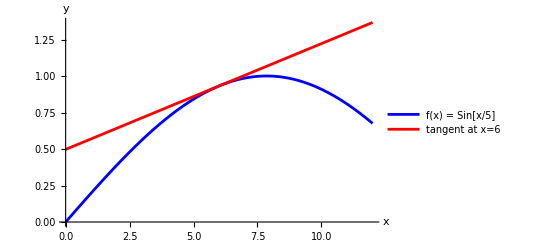

```mathematica
(*plot tangent line and f*)
Plot[{f[x],tangentline[x]},{x,0,12},PlotStyle->{Blue,Red},PlotLegends->{"f(x) = Sin[x/5]","tangent at x=6"},AxesLabel->{"x","y"}]
```

Zadanie 7.

```mathematica
ClearAll[f]
(*define the function*)
f[x_] := x^4 + 8x^3 -3x + 10;
```

```mathematica
(*solve for f(x) = 0*)
solutions = Solve[f[x] == 0, x, Reals];
```

```mathematica
N[solutions, 20]
```

{{x→-7.9322855603217923705},{x→-1.2708855224378163502}}

Zadanie 8.

```mathematica
ClearAll[f]
(*define the function*)
f[x_] := x^5 - 8x^3 - 2x - 6
```

```mathematica
(*find solutions*)
solutions = Reduce[f[x] >= 0, x, Reals];
N[solutions, 20]
```

-2.8256943696276903406≤x≤-0.83979199365047132273||x≥2.9118550201302351167

Zadanie 9.

```mathematica
ClearAll[f]
(*define the functions*)
f[x_] := 2Sin[x] - Log[x]
```

```mathematica
roots = FindRoot[f[x] == 0, {x, 2, 3}];
N[roots, 20]
```

{x→2.63571}

Zadanie 10.

```mathematica
ClearAll[f]
(*define the functions*)
f[x_] := Log[x^2 - 4] / (x - 1) ^ 2
f[x]
```

Log[-4+x^2]/(-1+x)^2

```mathematica
(*check the function domain, x^2-4 > 0, x-1 != 0*)
Reduce[x^2-4>0&&x!=1,x,Reals]
```

x<-2||x>2

```mathematica
(*check limits at both infinities and also in discontinuity points*)
```

```mathematica
Limit[f[x],x->-2,Direction->"FromBelow"]
```

-∞

```mathematica
Limit[f[x],x->2,Direction->"FromAbove"]
```

-∞

```mathematica
Limit[f[x],x->∞]
```

0

```mathematica
Limit[f[x],x->-∞]
```

0

```mathematica
(*check derivative and possible max and min points*)
```

```mathematica
f1[x_]:=D[f[x],x]//FullSimplify
f1[x]
```

(2 (((-1+x) x)/(-4+x^2)-Log[-4+x^2]))/(-1+x)^3

```mathematica
Solve[f1[x]==0&&(x<-2||x>2),x,Reals]
```

{{x→},{x→}}

```mathematica
Reduce[f1[x]>0&&(x<-2||x>2),x,Reals]
Reduce[f1[x]<0&&(x<-2||x>2),x,Reals]
```

2<x<||x<

x>||<x<-2

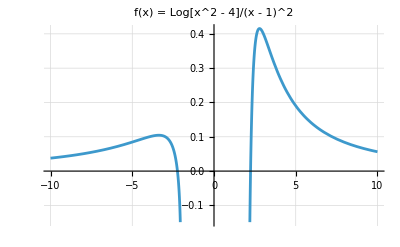

```mathematica
(*plot the functions on a graph*)
Plot[f[x],{x,-10,10},GridLines->Automatic,PlotLabel->"f(x) = Log[x^2 - 4]/(x - 1)^2"]
```